# Modellezés differenciálegyenletekkel

## Szabadesés légellenállással

V_T ((2 (V_T+V_0))/((V_T-V_0) ⅇ^((2 g t)/V_T)+V_T+V_0)-1)

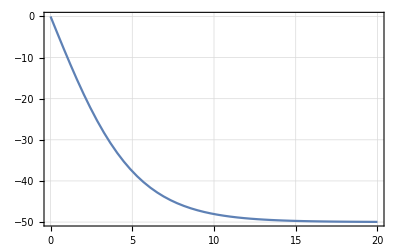

```mathematica
sol=DSolve[{v'[t]==-g+g/Subscript[V, T]^2 v[t]^2,v[0]==Subscript[V, 0]},v,t]//Quiet;
TraditionalForm[First[v[t]/.sol//FullSimplify]]
params={Subscript[V, T]->-50,g->9.8,Subscript[V, 0]->0};
Plot[Evaluate[v[t]/.sol/.params],{t,0,20},PlotTheme->"FrameGrid"]
```

```mathematica
Series[1-(v/Subscript[V, T])^2,{v,0,1}]//Normal
Series[1-(v/Subscript[V, T])^2,{v,Subscript[V, T],1}]//Normal//FullSimplify
```

1

2-(2 v)/V_T

```mathematica
sol1=DSolve[{v'[t]==-g,v[0]==Subscript[V, 0]},v,t]//Quiet;
sol2=DSolve[{v'[t]==-2 g (1-v[t]/Subscript[V, T]),v[0]==Subscript[V, T]+Subscript[V, 0]},v,t]//Quiet;
```

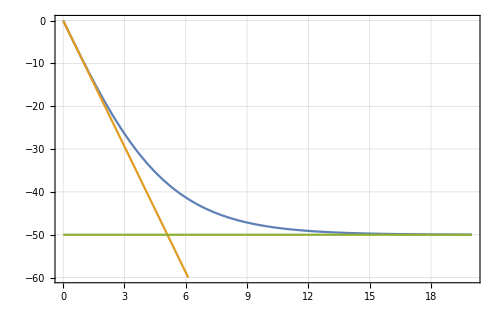

```mathematica
Plot[Evaluate[v[t]/.{sol,sol1,sol2}/.params],{t,0,20},PlotTheme->"FrameGrid",PlotRange->{-60,0}]
```

```mathematica
int=Integrate[First[v[t]/.sol],{t,0,τ}];
```

```mathematica
Solve[int==h,τ]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{τ→(Log[-(ⅇ^(-(g h)/V_T^2) V_T+√(V_0^2+(-1+ⅇ^(-(2 g h)/V_T^2)) V_T^2))/(V_0-V_T)] V_T)/g},{τ→(Log[(-ⅇ^(-(g h)/V_T^2) V_T+√(V_0^2+(-1+ⅇ^(-(2 g h)/V_T^2)) V_T^2))/(V_0-V_T)] V_T)/g}}

```mathematica
Solve[Integrate[First[v[t]/.sol1],{t,0,τ}]==h,τ]
```

{{τ→(V_0-√(-2 g h+V_0^2))/g},{τ→(V_0+√(-2 g h+V_0^2))/g}}